```mathematica
(*css zebrafinch model*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO) vI z +lsO qO ) + nh vh((1-lhO) vI z +lhO qO );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
(*leave Q in matrix different than one up above recursions*)
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO) vI z +lsO Q), vh((1-lhO) vI z +lhO Q ), 0, 0}, {vs((1-lsO) vI (1-z)+lsO(1- Q) ), vh((1-lhO) vI (1-z)+lhO(1- Q) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
Fasols=Solve[FFa==Fa,Fa]
```

{{Fa→(bn lhO u vh-bn lhO pn u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn u vs+bn pn vI vs-bn lsO pn vI vs-ba vh vI z+bn vh vI z+ba lhO vh vI z-bn lhO vh vI z+ba pa vh vI z-ba lhO pa vh vI z-bn pn vh vI z+bn lhO pn vh vI z-ba pa vI vs z+ba lsO pa vI vs z+bn pn vI vs z-bn lsO pn vI vs z-√(-4 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs) (bn vh vI z-bn lhO vh vI z-bn pn vh vI z+bn lhO pn vh vI z+bn pn vI vs z-bn lsO pn vI vs z)+(-bn lhO u vh+bn lhO pn u vh-bn vh vI+bn lhO vh vI+bn pn vh vI-bn lhO pn vh vI-bn lsO pn u vs-bn pn vI vs+bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z)^2))/(2 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs))},{Fa→(bn lhO u vh-bn lhO pn u vh+bn vh vI-bn lhO vh vI-bn pn vh vI+bn lhO pn vh vI+bn lsO pn u vs+bn pn vI vs-bn lsO pn vI vs-ba vh vI z+bn vh vI z+ba lhO vh vI z-bn lhO vh vI z+ba pa vh vI z-ba lhO pa vh vI z-bn pn vh vI z+bn lhO pn vh vI z-ba pa vI vs z+ba lsO pa vI vs z+bn pn vI vs z-bn lsO pn vI vs z+√(-4 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs) (bn vh vI z-bn lhO vh vI z-bn pn vh vI z+bn lhO pn vh vI z+bn pn vI vs z-bn lsO pn vI vs z)+(-bn lhO u vh+bn lhO pn u vh-bn vh vI+bn lhO vh vI+bn pn vh vI-bn lhO pn vh vI-bn lsO pn u vs-bn pn vI vs+bn lsO pn vI vs+ba vh vI z-bn vh vI z-ba lhO vh vI z+bn lhO vh vI z-ba pa vh vI z+ba lhO pa vh vI z+bn pn vh vI z-bn lhO pn vh vI z+ba pa vI vs z-ba lsO pa vI vs z-bn pn vI vs z+bn lsO pn vI vs z)^2))/(2 (-ba lhO u vh+bn lhO u vh+ba lhO pa u vh-bn lhO pn u vh-ba vh vI+bn vh vI+ba lhO vh vI-bn lhO vh vI+ba pa vh vI-ba lhO pa vh vI-bn pn vh vI+bn lhO pn vh vI-ba lsO pa u vs+bn lsO pn u vs-ba pa vI vs+ba lsO pa vI vs+bn pn vI vs-bn lsO pn vI vs))}}

```mathematica
subs = {ba->2,bn->1,z->.9,vs->.7,vh->.9,vI->.8  ,u->.01 , pa -> .1, pn-> .9}
test = {lsO->0 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2};
```

{ba→2,bn→1,z→0.9,vs→0.7,vh→0.9,vI→0.8,u→0.01,pa→0.1,pn→0.9}

```mathematica
Fasols[[1,1,2]]/.subs/.test (*check it is stable qhat with values, select positive q-hat*)
 Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs](*copy and past solution below*)
 Fasols/.subs/.test
```

0.874371

(0.0714818-0.426284 LHO+0.351824 LSO+0.413668 √(1.7551-3.07816 LHO+1.37523 LHO^2-0.412957 LSO+0.339848 LHO LSO+0.020996 LSO^2))/(0.688343-1. LHO+0.320261 LSO)

{{Fa→0.874371},{Fa→3.95373}}

```mathematica
QHAT[LHO_,LSO_] :=Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
```

```mathematica
AA
AA2=AA/.{Q->Qh}/.subs
```

{{0,0,ba pa,bn pn},{0,0,ba (1-pa),bn (1-pn)},{vs (lsO Q+(1-lsO) vI z),vh (lhO Q+(1-lhO) vI z),0,0},{vs (lsO (1-Q)+(1-lsO) vI (1-z)),vh (lhO (1-Q)+(1-lhO) vI (1-z)),0,0}}

{{0,0,0.2,0.9},{0,0,1.8,0.1},{0.7 (0.72 (1-lsO)+lsO Qh),0.9 (0.72 (1-lhO)+lhO Qh),0,0},{0.7 (0.08 (1-lsO)+lsO (1-Qh)),0.9 (0.08 (1-lhO)+lhO (1-Qh)),0,0}}

```mathematica
LL=Eigenvalues[AA2];
```

```mathematica
Eigenvalues[AA2]/.subs/.test /.Qh-> 0.5
```

{-1.12813,1.12813,0.-0.450288 ⅈ,0.+0.450288 ⅈ}

```mathematica
(*should i substitute Qhat for home condition in before eigenvalues?, also see if i can find positive one automatically*)
```

```mathematica
(*isolate Dominant eigenvalue, substitute in q-hat*)
Lambda1[ lsO_, lhO_,LHO_,LSO_]:= Simplify[LL[[2]]/.Qh->  QHAT[LHO,LSO]];
```

```mathematica
(*take partial derivatives, substitute mutant for common type*)
DlsO=D[Lambda1[lsO, lhO,LHO,LSO],lsO]/. {LHO -> lhO,LSO-> lsO};
```

```mathematica
DlhO=D[Lambda1[lsO, lhO,LHO,LSO],lhO]/. {LHO -> lhO,LSO-> lsO};
```

```mathematica
(*try and graph*)

lsOstart=0.01;
lhOstart=0.5;
imax=1000;
lsItab=Table[0,{i,imax}];
lhItab=Table[0,{i,imax}];
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.04;
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;

DlsOtab[[1]]=DlsO/.subs/.{lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.subs/.{lsO->lsOstart,lhO->lhOstart};
```

```mathematica
For[i=2,i<imax,i++,{

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsOtab[[i]]=DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];
```

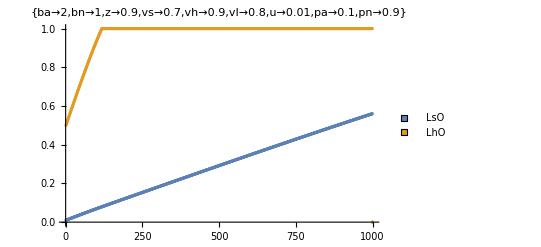

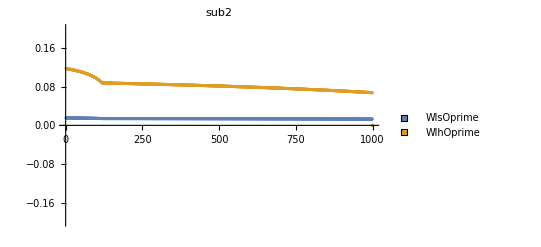

```mathematica
ListPlot[{lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsO,LhO},LegendMarkers->Graphics[Rectangle[]]],PlotLabel->subs] 
ListPlot[{DlsOtab,DlhOtab},PlotRange->{All,{-0.2,0.2}},PlotLegends->PointLegend[{WlsOprime,WlhOprime},LegendMarkers->Graphics[Rectangle[]]],PlotLabel->sub2]
```